```mathematica
ClearAll["`*"];
```

```mathematica
$HistoryLength = 0;
```

```mathematica
list1 = {};
```

```mathematica
SetAttributes[append, HoldFirst];
```

```mathematica
append[list_, item_] := 
list = Append[list, item];
```

```mathematica
appendTime = 
Table[{i, AbsoluteTiming[append[list1, i]][[1]]}, {i, 1, 5000}];
```

```mathematica
SetAttributes[remove, HoldFirst];
```

```mathematica
remove[list_Symbol] := 
list = Delete[list, -1];
```

```mathematica
list1 = {};
```

```mathematica
removeTime = Table[
	{
		i, 
		append[list1, i]; 
		append[list1, i]; 
		AbsoluteTiming[remove[list1]][[1]]
	}, 
	{i, 1, 5000}
];
```

```mathematica
part[list_, i_] := 
list[[i]];
```

```mathematica
list1 = {};
```

```mathematica
partTime = 
Table[
	{
		i, 
		append[list1, i]; 
		With[{j = RandomInteger[{1, i}]},  
			AbsoluteTiming[part[list1, j]][[1]]
		]
	}, 
	{i, 1, 5000}
];
```

```mathematica
SetAttributes[insert, HoldFirst];
```

```mathematica
insert[list_, item_, i_] := 
list = Insert[list, item, i];
```

```mathematica
list1 = {1};
```

```mathematica
insertTime = 
Table[
	{
		i, 
		With[{j = RandomInteger[{1, i}]},  
			AbsoluteTiming[insert[list1, i, j]][[1]]
		]
	}, 
	{i, 1, 5000}
];
```

```mathematica
position[list_, item_] := 
Position[list, item];
```

```mathematica
list1 = {1};
```

```mathematica
positionTime = 
Table[
	{
		i, 
		With[{j = RandomInteger[{1, i}]},  
			insert[list1, i, j]; 
			AbsoluteTiming[position[list1, i]][[1]]
		]
	}, 
	{i, 1, 5000}
];
```

```mathematica
ListPlot[{appendTime, removeTime, insertTime}, 
	PlotLegends -> {"append", "remove", "insert"}, 
	ImageSize -> Large, 
	PlotTheme -> "Detailed"
]
```

```mathematica
ListPlot[{positionTime}, 
	PlotLegends -> {"position"}, 
	ImageSize -> Large, 
	PlotTheme -> "Detailed"
]
```

```mathematica
ListPlot[{partTime}, 
	PlotLegends -> {"part"}, 
	ImageSize -> Large, 
	PlotTheme -> "Detailed"
]
```

```mathematica
ClearAll[DynamicList];
```

```mathematica
SetAttributes[DynamicList, HoldFirst]
```

```mathematica
createDynamicList[] := 
With[{ref = Unique["DYNAMICLIST`$"]}, 
	ref = <|
		"Data" -> {0}, 
		"Length" -> 0, 
		"Capacity" -> 1
	|>; 
	DynamicList[ref]
];
```

```mathematica
ClearAttributes[append, HoldFirst];
```

```mathematica
DynamicList /: append[DynamicList[ref_Symbol], item_] := 
With[{len = ref["Length"], capacity = ref["Capacity"]}, 
	If[len === capacity, 
		ref["Data"] = Join[ref["Data"], ConstantArray[0, len]]; 
		ref["Capacity"] = capacity * 2; 
	]; 
	ref["Length"] = len + 1; 
	ref[["Data", len + 1]] = item
];
```

```mathematica
ClearAttributes[remove, HoldFirst];
```

```mathematica
DynamicList /: remove[DynamicList[ref_Symbol]] := 
With[{
	len = ref["Length"], 
	capacity = ref["Capacity"], 
	item = ref[["Data", ref["Length"]]]
}, 
	If[len === capacity / 2, 
		ref["Data"] = ref[["Data", ;; capacity / 2]]; 
		ref["Capacity"] = capacity / 2; 
	]; 
	ref["Length"] = len - 1; 
	ref[["Data", len]] = 0; 
	item
];
```

```mathematica
ClearAttributes[insert, HoldFirst];
```

```mathematica
DynamicList /: insert[DynamicList[ref_Symbol], item_, i_Integer] := 
With[{len = ref["Length"], capacity = ref["Capacity"]}, 
	If[len === capacity, 
		ref["Data"] = Join[ref["Data"], ConstantArray[0, len]]; 
		ref["Capacity"] = capacity * 2;  
	]; 
	ref["Length"] = len + 1; 
	ref[["Data"]] = Join[ref[["Data", 1 ;; i - 1]], {item}, ref[["Data", i ;; -2]]]; 
	item
];
```

```mathematica
DynamicList /: position[DynamicList[ref_Symbol], item_] := 
Position[ref[["Data", 1 ;; ref["Length"]]], item];
```

```mathematica
DynamicList /: part[DynamicList[ref_Symbol], i_Integer] := 
If[Abs[i] <= ref["Length"], ref[["Data", i]], Message[General::partw, i, DynamicList[ref]]];
```

```mathematica
DynamicList /: Normal[DynamicList[ref_Symbol]] := 
ref[["Data", 1 ;; ref["Length"]]];
```

```mathematica
DynamicList /: DeleteObject[DynamicList[ref_Symbol]] := 
ClearAll[ref];
```

```mathematica
$dynamicListIcon = Import["https://wolfr.am/1jEFx2BBO"];
```

```mathematica
DynamicList /: MakeBoxes[object: DynamicList[ref_Symbol], 
	form: (StandardForm | TraditionalForm)] := 
Module[{above, below}, 
	above = {
		{BoxForm`SummaryItem[{"Ref: ", Defer[ref]}], SpanFromLeft}, 
		{BoxForm`SummaryItem[{"Length: ", ref["Length"]}], SpanFromLeft}, 
		{BoxForm`SummaryItem[{"Capacity: ", ref["Capacity"]}], SpanFromLeft}
	}; 
	below = {}; 
	
	BoxForm`ArrangeSummaryBox[
		DynamicList, 
		object, 
		$dynamicListIcon, 
		above, 
		below, 
		form, 
		"Interpretable" -> Automatic
	]
];
```

```mathematica
dynamicList1 = createDynamicList[]
```

```mathematica
append[dynamicList1, #]& /@ Range[10]
```

```mathematica
Do[remove[dynamicList1], {3}]
```

```mathematica
Normal[dynamicList1]
```

```mathematica
DeleteObject[dynamicList1]
```

```mathematica
dynamicList1[[1]]
```

```mathematica
DeleteObject[dynamicList1];
```

```mathematica
dynamicList1 = createDynamicList[];
```

```mathematica
appendTime = 
Table[{i, AbsoluteTiming[append[dynamicList1, i]][[1]]}, {i, 1, 5000}];
```

```mathematica
DeleteObject[dynamicList1];
```

```mathematica
dynamicList1 = createDynamicList[];
```

```mathematica
removeTime = Table[
	{
		i, 
		append[dynamicList1, i]; 
		append[dynamicList1, i]; 
		AbsoluteTiming[remove[dynamicList1]][[1]]
	}, 
	{i, 1, 5000}
];
```

```mathematica
ListPlot[{appendTime, removeTime}, 
	PlotLegends -> {"append", "remove"}, 
	ImageSize -> Large, 
	PlotTheme -> "Detailed"
]
```

```mathematica
DeleteObject[dynamicList1];
```

```mathematica
dynamicList1 = createDynamicList[];
```

```mathematica
insertTime = 
Table[
	{
		i, 
		With[{j = RandomInteger[{1, i}]},  
			AbsoluteTiming[insert[dynamicList1, i, j]][[1]]
		]
	}, 
	{i, 1, 5000}
];
```

```mathematica
DeleteObject[dynamicList1];
```

```mathematica
dynamicList1 = createDynamicList[];
```

```mathematica
positionTime = 
Table[
	{
		i, 
		With[{j = RandomInteger[{1, i}]},  
			insert[dynamicList1, i, j]; 
			AbsoluteTiming[position[dynamicList1, i]][[1]]
		]
	}, 
	{i, 1, 5000}
];
```

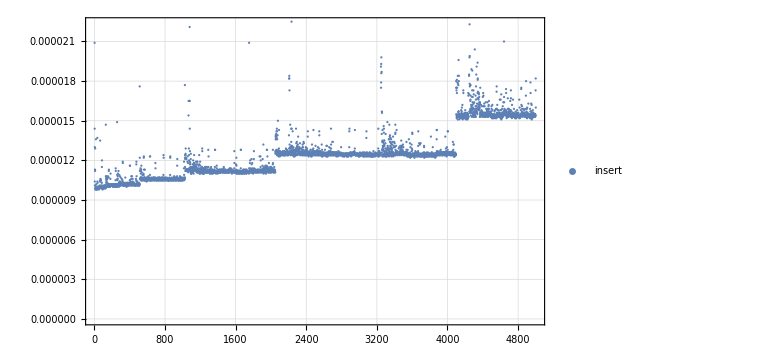

```mathematica
ListPlot[{insertTime}, 
	PlotLegends -> {"insert"}, 
	ImageSize -> Large, 
	PlotTheme -> "Detailed"
]
```

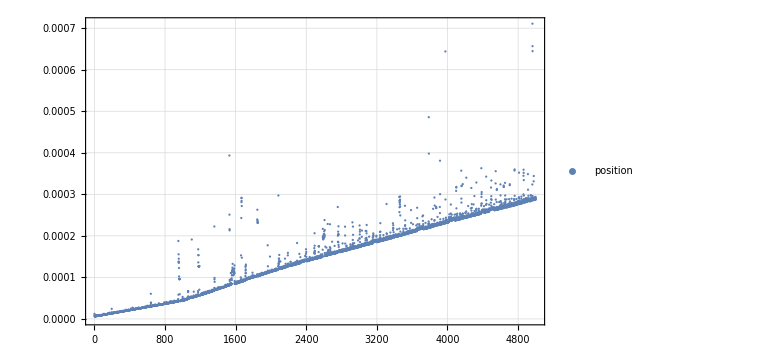

```mathematica
ListPlot[{positionTime}, 
	PlotLegends -> {"position"}, 
	ImageSize -> Large, 
	PlotTheme -> "Detailed"
]
```